## SVD Unit Tests

```mathematica
SetDirectory[NotebookDirectory[]];
getTransSVD[ptsSrc_,ptsTgt_]:=Module[{cent1,cent2,matP,matQ,mat,u,w,v,r,func,vec},
(* getting the centroid *)
cent1=Mean[ptsSrc];
cent2=Mean[ptsTgt];

(* forming the cross-covariance matrix *)
matP=Map[(#-cent1)&,ptsSrc];
matQ=Map[(#-cent2)&,ptsTgt];
mat=Transpose[matP].matQ;

(* SVD decomposition *)
{u,w,v}=SingularValueDecomposition[mat];

(* obtaining the rotation *)
r=v.Transpose[u];
vec=cent2-cent1;
(* transform *)
func[pts_]:=Module[{npts,nmat,ncent},
ncent=Mean[pts];(*I think this line is a bug. I believe that this is corrected with the following line.*)
ncent=cent1;
nmat=Map[(#-ncent)&,pts];
npts=Transpose[r.Transpose[nmat]];
Map[(#+vec+ncent)&,npts]];

func];
```

```mathematica
(*Generate random points to test on in c++*)
RandomSeed[0];
randReal [e_]:=RandomReal[{-e,e}];
perturb[pts_,e_]:=Map[(Map[(#+RandomReal[{-e,e}])&,#])&,pts];
genSVDTest [n_]:=Module[{alignSource, alignTarget, mapSource, mapTest, randVec}, 
alignSource = Map[(Map[(RandomReal[{-100,100}])&,Range[2]])&,Range[5]]//N;
randVec = {randReal[100], randReal[100]};
(*Rotate, then translate, then add random noise*)
alignTarget = perturb[Map[(#+randVec)&,Transpose[RotationMatrix[randReal[π]].Transpose[alignSource]]], randReal[10]]//N;
mapSource = Map[(Map[(RandomReal[{-100,100}])&,Range[2]])&,Range[n]] //N;
 mapTest = getTransSVD[alignSource,alignTarget][mapSource]//N;
{alignSource, alignTarget, mapSource, mapTest}
]
```

```mathematica
(*Generate tests, then export them to the selected file*)
svdTests = Map[(genSVDTest[#*10])&,Range[250]]//N
(*Export["C:\\Users\\Aiden McIlraith\\Documents\\GitHub\\st-visualizer\\UnitTest\\svd.json", svdTests];*)
```

{{{{-27.4426,7.88241},{-94.6587,-12.3466},{-86.3357,-6.21674},{-15.1894,-83.1945},{67.9071,-75.6147}},{1},{1},{{-8.10395,-14.2131},{-20.7642,124.904},{4.3007,41.7972},4,{-102.069,3.65755},{-31.6139,116.613},{-39.938,94.735}}},248,{1}}
 |  |  |  |

## Grow and Cover Unit Tests

### Utility Functions

```mathematica
ϵ=0.2;
rotM[a_]:=N[{{Cos[a],-Sin[a]},{Sin[a],Cos[a]}}];
hexM=N[rotM[π/3]];
```

```mathematica
getCoords[pt_,origin_,v1_,v2_]:=Inverse[Transpose[{v1,v2}]].(pt-origin);
getPt[coords_,origin_,v1_,v2_]:=coords.{v1,v2}+origin;
```

### Init Functions

```mathematica
getInliers[pts_,{origin_,vec_}]:=Module[{intcoords,vec2=hexM.vec,inds},
intcoords=Map[Round[getCoords[#,origin,vec,vec2]]&,pts];
inds=Select[Range[Length[pts]],(Norm[pts⟦#⟧-getPt[intcoords⟦#⟧,origin,vec,vec2]]<ϵ*Norm[vec])&];
{inds,intcoords⟦inds⟧}];
```

```mathematica
initGridInliers[pts_,num_]:=Module[{ori,v,in={{},{}},oriTemp,vTemp,inTemp},
Do[oriTemp=RandomSample[pts,1]⟦1⟧;
vTemp=Nearest[pts,oriTemp,2]⟦2⟧-oriTemp;
inTemp=getInliers[pts,{oriTemp,vTemp}];
If[Length[inTemp⟦1⟧]>Length[in⟦1⟧],
ori=oriTemp;
v=vTemp;
in=inTemp],
{i,num}];
{{ori,v},in}];
```

```mathematica
getGrid[pts_,{inds_,intcoords_}]:=Module[{ata=Table[0,{4},{4}],atb=Table[0,{4}],a,I2=IdentityMatrix[2],res},
Do[
a=Transpose[Join[Transpose[intcoords⟦i,1⟧*I2+intcoords⟦i,2⟧*hexM],I2]];
ata+=Transpose[a].a;
atb+=Transpose[a].pts⟦inds⟦i⟧⟧,
{i,Length[inds]}
];
res=Inverse[ata].atb;
(*Origin, V1*)
{res⟦{3,4}⟧,res⟦{1,2}⟧}];
```

```mathematica
refineGrid[pts_,grid_,inliers_]:=Module[{newGrid=grid,newInliers=inliers,num=Length[inliers⟦1⟧]},
While[num<Length[pts],
(* Print["Iterate"]; *)
newGrid=getGrid[pts,newInliers];
newInliers=getInliers[pts,newGrid];
If[Length[newInliers⟦1⟧]>num,
num=Length[newInliers⟦1⟧],
Break[]]];
newGrid=getGrid[pts,newInliers];
{newGrid,newInliers}];
```

```mathematica
getGridAndCoords[pts_,num_]:=Module[{grid,inliers,v2},
{grid,inliers}=initGridInliers[pts,num];
{grid,inliers}=refineGrid[pts,grid,inliers];
v2=hexM.grid⟦2⟧;
{grid,Map[Round[getCoords[#,grid⟦1⟧,grid⟦2⟧,v2]]&,pts]}];
```

### Init Functions Tests (pulls from hexfit.json)

```mathematica
(*Test Function*)
getRangeRatio[pts_,r_]:=Map[{(1-r)Mean[#]+r#⟦1⟧,(1-r)Mean[#]+r#⟦2⟧}&,Transpose[{Map[Min,Transpose[pts]],Map[Max,Transpose[pts]]}]];
drawFit[pts_,{origin_,vec_},intcoords_,ptSize_]:=Module[{r=getRangeRatio[pts,1.2],rcoords,lx,hx,ly,hy,vec2=hexM.vec,inds, outinds},
inds=getInliers[pts,{origin,vec}][[1]];
outinds=Complement[Range[Length[pts]],inds];
rcoords=Map[Round[getCoords[#,origin,vec,vec2]]&,{{r⟦1,1⟧,r⟦2,1⟧},{r⟦1,1⟧,r⟦2,2⟧},{r⟦1,2⟧,r⟦2,1⟧},{r⟦1,2⟧,r⟦2,2⟧}}];
{lx,ly}=Map[Min,Transpose[rcoords]];
{hx,hy}=Map[Max,Transpose[rcoords]];

Graphics[{
{LightGray,Table[Line[{getPt[{x,ly},origin,vec,vec2],getPt[{x,hy},origin,vec,vec2]}],{x,lx,hx}],
Table[Line[{getPt[{lx,y},origin,vec,vec2],getPt[{hx,y},origin,vec,vec2]}],{y,ly,hy}]},
(* calculated grid points *)
{Blue,AbsolutePointSize[ptSize],Map[Point[getPt[#,origin,vec,vec2]]&,intcoords]},
(* outlier points *)
{Red, AbsolutePointSize[ptSize],Map[Point,pts⟦outinds⟧]},
(* inlier points *)
{Green, AbsolutePointSize[ptSize],Map[Point,pts⟦inds⟧]},
(* grid *)
{Black, AbsolutePointSize[ptSize*2],Point[origin]},
{Black,AbsoluteThickness[ptSize],Line[{origin,origin+vec}]}

},
PlotRange->r]];
```

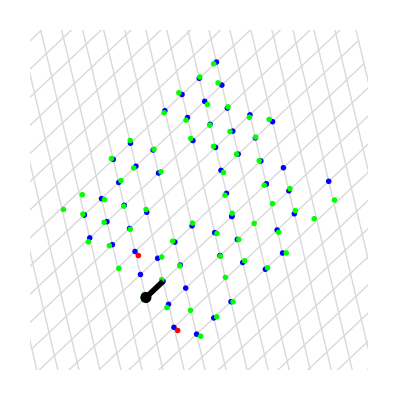
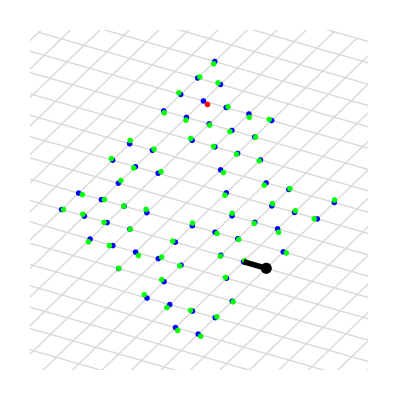
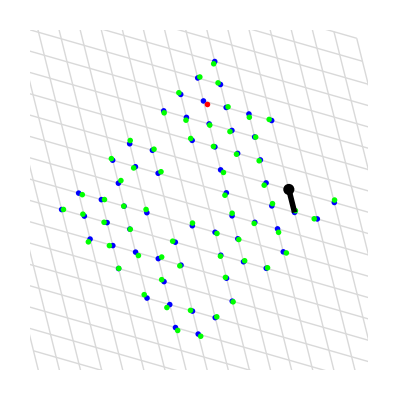
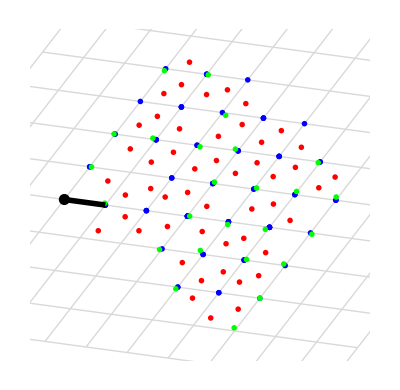
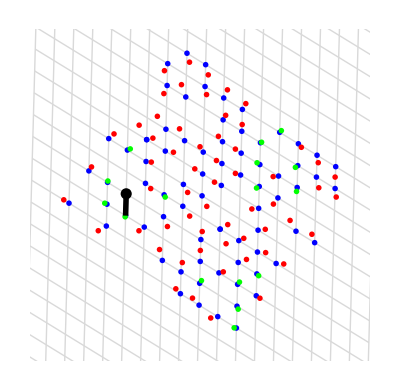
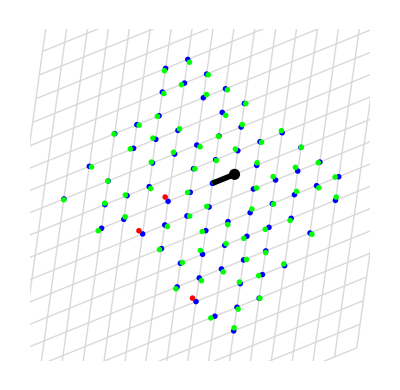
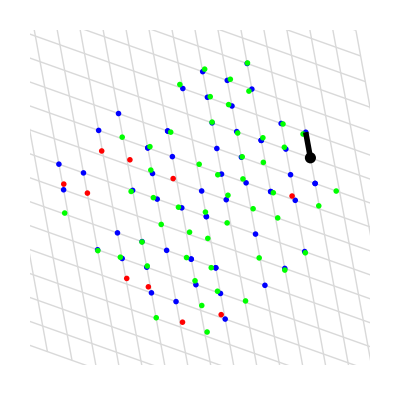
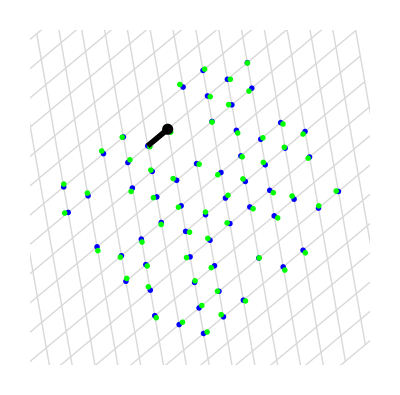

```mathematica
importedData = Import["C:\\Users\\Aiden McIlraith\\Documents\\GitHub\\st-visualizer\\hexResults.json"];
importedPlots=Map[(drawFit[#[[1]],#[[2]],#[[3]],4])&,importedData];
mathematicaPlots:=Map[(drawFit[#[[1]],#[[2]][[1]],#[[2]][[2]],4])&,Map[({#[[1]],getGridAndCoords[#[[1]], 10]})&,importedData]];
Column[Transpose[{importedPlots,mathematicaPlots,mathematicaPlots}]]
```

### The Grow Function

```mathematica
growAndCover[pts_,samples_,wid_,num_]:=Module[{hash,ncoords={},grid,coords,loc,nghbs={{1,0},{0,1},{-1,1},{-1,0},{0,-1},{1,-1}},nghbs2,v2,bd,nbd},
(* Compute grid and coordinates *)
{grid,coords}=getGridAndCoords[pts,num];
v2=hexM.grid⟦2⟧;

(* Store existing points in hash *)
hash[_,_]=False;
Scan[(hash[#⟦1⟧,#⟦2⟧]=True)&,coords];

(* for each sample, if its nearest grid point and or any of its 6-neighbors are not in the list, add them to the list *)
nghbs2=Append[nghbs,{0,0}];
Scan[
(
loc=Round[getCoords[#,grid⟦1⟧,grid⟦2⟧,v2]];
Scan[
If[!(Apply[hash,loc+#]),
hash[loc⟦1⟧+#⟦1⟧,loc⟦2⟧+#⟦2⟧]=True;
AppendTo[ncoords,loc+#]
]&
,nghbs2])&
,samples];

(* growing *)
bd=Join[coords,ncoords]; (* queue of points added in the previous iteration *)
Do[
nbd={}; (* queue of points added in this iteration *)
Scan[
(loc=#;
Scan[If[!(Apply[hash,loc+#]),
hash[loc⟦1⟧+#⟦1⟧,loc⟦2⟧+#⟦2⟧]=True;
AppendTo[ncoords,loc+#];
AppendTo[nbd,loc+#]]&,nghbs])&,
bd];
bd=nbd,
{i,wid}];

Map[getPt[#,grid⟦1⟧,grid⟦2⟧,v2]&,ncoords]];
```

```mathematica
(*Use thresholded deviation from point grid to unit text hexfit functionality*)
```

### Grow Tests

```mathematica
pts={{1,1},{2,2},{3,3}}
```

{{1,1},{2,2},{3,3}}

```mathematica
SeedRandom[0];
samples={{3,7},{2,9},{6,4},{1,8}};
npts0=growAndCover[pts,samples,0,50];
```

```mathematica
SeedRandom[0];
samples={{3,7},{2,9},{6,4},{1,8}};
npts1=growAndCover[pts,samples,1,50];
```

```mathematica
SeedRandom[0];
samples={{3,7},{2,9},{6,4},{1,8}};
npts2=growAndCover[pts,samples,2,50];
```

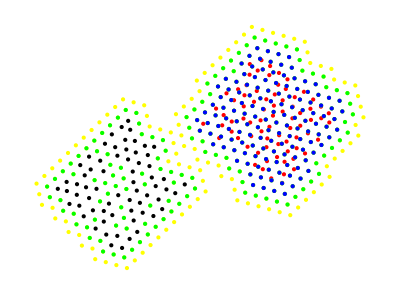
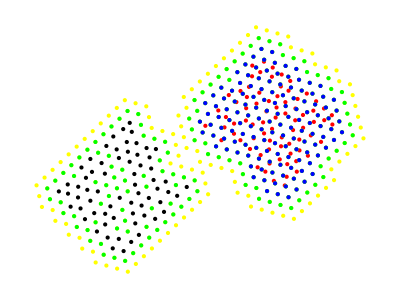
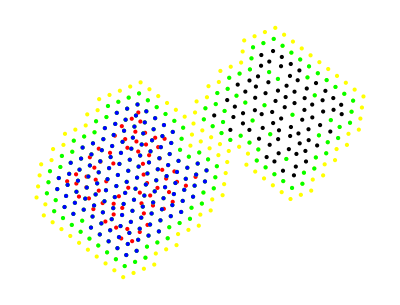
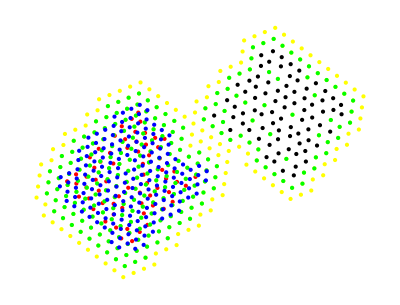
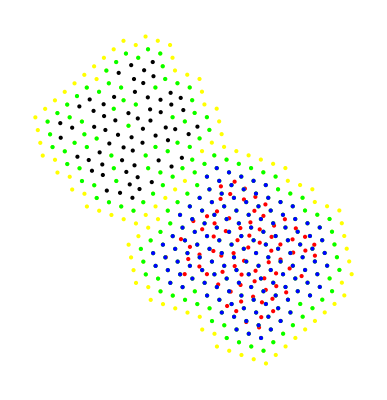
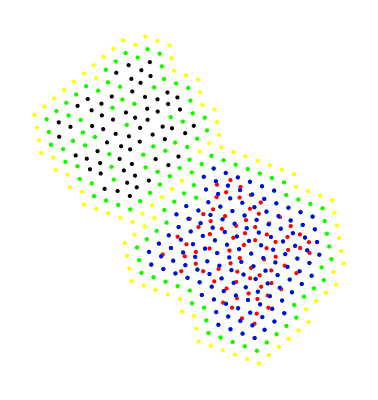
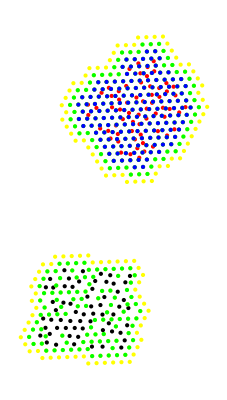
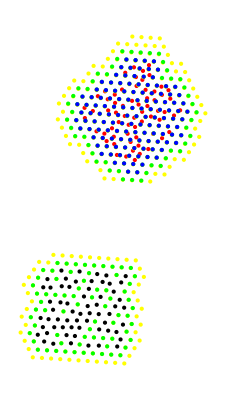

```mathematica
graphGrow[pts_,samples_,npts0_,npts1_, npts2_]:=Module[{},
Graphics[{Map[Point,pts],{Red,Map[Point,samples]},{Yellow,Map[Point,npts2]},{Green,Map[Point,npts1]},{Blue,Map[Point,npts0]}}]
];
importedData = Import["C:\\Users\\Aiden McIlraith\\Documents\\GitHub\\st-visualizer\\growResults.json"];
importedPlots:=Map[(graphGrow[#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]])&,importedData];
mathematicaPlots:=Map[(graphGrow[
#[[1]],#[[2]],
growAndCover[#[[1]],#[[2]],0,50],
growAndCover[#[[1]],#[[2]],1,50],
growAndCover[#[[1]],#[[2]],2,50]
])&,importedData];
Column[Transpose[{importedPlots,mathematicaPlots}]]
```

## TSV Import Unit Tests

### Functions

```mathematica
getClusterArray[n_,i_]:=Module[{arr=Table[0,{n}]},arr⟦i⟧=1;arr];
numRANSAC=5;
widBuffer=2;
```

```mathematica
loadTSV[fname_,sliceNames_,sliceInd_,tissueInd_,rowcolInds_,clusterInd_,featureInds_,zDis_,srctgts_]:=Module[{slices,vals,clusters,tab,records,nclusters,nfeatures,nm,xyInds=Reverse[rowcolInds],names,nslices},
tab=Import[fname];
names=Append[tab⟦1,featureInds⟧,"No tissue"];
tab=Drop[tab,1];

nclusters = Max[Select[tab⟦;;,clusterInd⟧,NumberQ]]+1;
nfeatures=Length[featureInds];
records=Map[(nm=#;Select[tab,(#⟦sliceInd⟧==nm&&#⟦tissueInd⟧==1)&])&,sliceNames];
slices=Table[
If[i==1,
records⟦i,;;,xyInds⟧,
getTransSVD[srctgts⟦i-1,1⟧,srctgts⟦i-1,2⟧][records⟦i,;;,xyInds⟧]],
{i,Length[sliceNames]}];
clusters=Map[Map[If[#⟦tissueInd⟧==0,
getClusterArray[nclusters+1,nclusters+1],
getClusterArray[nclusters+1,#⟦clusterInd⟧+1]]&,#]&,records];
vals=Map[Map[If[#⟦tissueInd⟧==0,
getClusterArray[nfeatures+1,nfeatures+1],
Append[#⟦featureInds⟧,0]]&,#]&,records];

(* Add buffer to each slice and cover neighboring slices *)
nslices=Table[
Switch[i,
1,
growAndCover[slices⟦i⟧,slices⟦i+1⟧,widBuffer,numRANSAC],
Length[slices],
growAndCover[slices⟦i⟧,slices⟦i-1⟧,widBuffer,numRANSAC],
_,
growAndCover[slices⟦i⟧,Join[slices⟦i-1⟧,slices⟦i+1⟧],widBuffer,numRANSAC]],{i,Length[slices]}];

slices=Table[Map[Append[#,i*zDis]&,Join[slices⟦i⟧,nslices⟦i⟧]],{i,Length[slices]}];
clusters=MapThread[Join[#1,Map[getClusterArray[nclusters+1,nclusters+1]&,#2]]&,{clusters,nslices}];
vals=MapThread[Join[#1,Map[getClusterArray[nfeatures+1,nfeatures+1]&,#2]]&,{vals,nslices}];

(* add empty top and bottom slices *)
slices=Prepend[Append[slices,Map[(#+{0,0,zDis})&,Last[slices]]],Map[(#+{0,0,-zDis})&,First[slices]]];
clusters=
Prepend[Append[clusters,
Map[getClusterArray[nclusters+1,nclusters+1]&,Last[slices]]],
Map[getClusterArray[nclusters+1,nclusters+1]&,First[slices]]];
vals=
Prepend[Append[vals,
Map[getClusterArray[nfeatures+1,nfeatures+1]&,Last[slices]]],
Map[getClusterArray[nfeatures+1,nfeatures+1]&,First[slices]]];

{slices,clusters,vals,names}
]
```

```mathematica
Dimensions[clusters[[4]]]
```

Part::partd: Part specification clusters⟦4⟧ is longer than depth of object.

{2}

### Unit Tests